## GeneticAlgorithm to fit an ellipse inside a random polygon

```mathematica
Get[FileNameJoin[{NotebookDirectory[], "GeneticAlgorithmPackage.wl"}]]
```

```mathematica
finalPoints = {{-1.683623649588597,9.512948638668554},{4.0321421508223025,6.897869670971218},{7.892631139769513,9.126740893617487},{2.71288528330998,-6.293271537107401},{0.850933266410042,2.950743070326915}};
polygon = Polygon[finalPoints];
polygonArea = Area[Region[polygon]];

EllipseFitness[elist_] :=
	Module[{ellipse},
		ellipse = Disk[{elist[[1]], elist[[2]]}, {elist[[3]], elist[[4]]}];
		Area[Region[RegionIntersection[ellipse, polygon]]]
	] 

EllipseConstraint[elist_] :=
	Module[{ellipse},
		ellipse = Disk[{elist[[1]], elist[[2]]}, {elist[[3]], elist[[4]]}];
		Area[Region[RegionUnion[ellipse, polygon]]] == polygonArea
	]
```

```mathematica
ClearAll[init];
init = {2, 4, 1, 1}
resultEllipse = GeneticAlgorithm[init, EllipseFitness, {EllipseConstraint}] // Column

Show[Graphics[{Blue, polygon}], Graphics[{Yellow, Disk[{#[[1]], #[[2]]}, {#[[3]], #[[4]]}]}]]& /@ First[First[resultEllipse]] // Row
Show[Graphics[{Blue, polygon}], Graphics[{Yellow, Disk[{#[[1]], #[[2]]}, {#[[3]], #[[4]]}]}]]& /@ Last[First[resultEllipse]] // Row
```

{2,4,1,1}

population = {{2,4,1,1},{1.78941,4.14269,1.13062,0.964036},{1.76265,4.1595,1.0853,1.19553}}

population = {{2.22333,4.01615,0.969338,1.1842},{1.77916,4.43195,1.29047,1.18304},{1.72704,3.88009,1.11497,0.760773}}

population = {{2.22333,4.01615,0.969338,1.1842},{1.72704,3.88009,1.11497,0.760773},{1.97212,4.09948,0.787897,1.26591}}

population = {{2.30529,3.97443,1.17028,1.14881},{2.05589,4.10672,0.830231,1.36842},{1.97212,4.09948,0.787897,1.26591}}

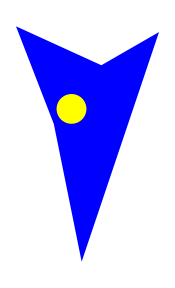

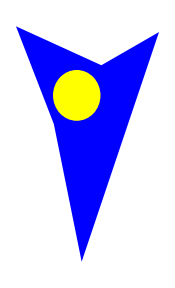

```mathematica
Show[Graphics[{Blue, polygon}], Graphics[{Yellow, Disk[{2, 4},{1, 1}]}]]
Show[Graphics[{Blue, polygon}], Graphics[{Yellow, Disk[{2.351453808437171,4.9080560965437865},{1.5898728053797293,1.7075110680894408}]}]]
```